53

-9.27953+0.303433 x

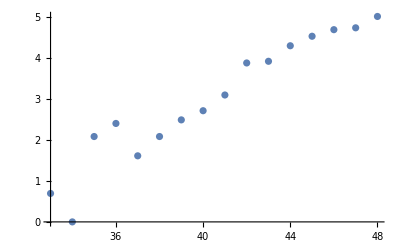

-0.73899

```mathematica
X= {1,1,0,0,0,1,1,2,1,1,1,0,2,2,4,3,2,0,2,2,2,2,3,1,3,2,0,5,3,6,2,1,2,1,8,11,5,8,12,15,22,48,50,73,92,108,113,149,123,97,75,34,6};
n=Length[X]
Fit[Table[{t,Log[X[[t]]]},{t,33,48}],{1,x},x]
Show[Plot[%,{t,33,48}],ListPlot[Table[{t,Log[X[[t]]]},{t,33,48}]]]
(Mean[Table[X[[t]]t,{t,33,48}]]-42.5Mean[Table[X[[t]],{t,33,48}]])/(Mean[Table[t^2,{t,33,48}]]-42.5^2)
```